```mathematica
Mat = {{1,1-Γ,1-Γ,1-Γ},{2(1-Γ), 2, 2(1-Γ), 2(1-Γ)},{3(1-Γ), 3, 3(1-Γ), 3(1-Γ)},{4(1-Γ), 4, 4(1-Γ), 4(1-Γ)}}
```

{{1,1-Γ,1-Γ,1-Γ},{2 (1-Γ),2,2 (1-Γ),2 (1-Γ)},{3 (1-Γ),3,3 (1-Γ),3 (1-Γ)},{4 (1-Γ),4,4 (1-Γ),4 (1-Γ)}}

```mathematica
es = Eigensystem[Mat]
```

{{0,0,1/2 (10-7 Γ-√(100-184 Γ+85 Γ^2)),1/2 (10-7 Γ+√(100-184 Γ+85 Γ^2))},{{-(-1+Γ)/(-2+Γ),-(-1+Γ)/(-2+Γ),0,1},{-(-1+Γ)/(-2+Γ),-(-1+Γ)/(-2+Γ),1,0},{-(-8+7 Γ-√(100-184 Γ+85 Γ^2))/(8 (-1+Γ)),1/2,3/4,1},{-(-8+7 Γ+√(100-184 Γ+85 Γ^2))/(8 (-1+Γ)),1/2,3/4,1}}}

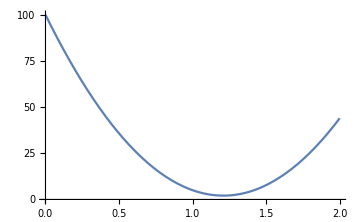

```mathematica
Plot[(1/2 (10-7 Γ-√(100-184 Γ+85 Γ^2)))^n+(1/2 (10-7 Γ+√(100-184 Γ+85 Γ^2)))^n/.n->2,{Γ,0,2}]
```

```mathematica
Mat1 = {-3/2*{1,1-Γ,1-Γ,1-Γ},-1/2*{1-Γ,1,1-Γ,1-Γ},1/2*{1-Γ,1-Γ,1,1-Γ},3/2*{1-Γ,1-Γ,1-Γ,1} }
es = Eigensystem[Mat1]
```

{{-3/2,-3/2 (1-Γ),-3/2 (1-Γ),-3/2 (1-Γ)},{1/2 (-1+Γ),-1/2,1/2 (-1+Γ),1/2 (-1+Γ)},{(1-Γ)/2,(1-Γ)/2,1/2,(1-Γ)/2},{(3 (1-Γ))/2,(3 (1-Γ))/2,(3 (1-Γ))/2,3/2}}

{{-1/2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))),1/2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))),-1/2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))),1/2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))},{{-((2 (-15 Γ+12 Γ^2-3 Γ^3+3 √(Γ^2 (25-34 Γ+13 Γ^2))-4 Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+2 Γ^2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+√(Γ^2 (25-34 Γ+13 Γ^2)) √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))))/(3 (-1+Γ) (-Γ+√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))) (Γ+√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))))),-((3 Γ-3 Γ^2+√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))-Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(-3 Γ+3 Γ^2+3 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))-3 Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))),-(-3 Γ+3 Γ^2-√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(3 Γ-3 Γ^2+3 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))-3 Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))),1},{-((2 (15 Γ-12 Γ^2+3 Γ^3-3 √(Γ^2 (25-34 Γ+13 Γ^2))-4 Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+2 Γ^2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+√(Γ^2 (25-34 Γ+13 Γ^2)) √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))))/(3 (-1+Γ) (Γ-√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))) (Γ+√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))))),-((3 Γ-3 Γ^2-√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(-3 Γ+3 Γ^2-3 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+3 Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))),-(-3 Γ+3 Γ^2+√(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))-Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(3 Γ-3 Γ^2-3 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))+3 Γ √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2)))),1},{(2 (15 Γ-12 Γ^2+3 Γ^3+3 √(Γ^2 (25-34 Γ+13 Γ^2))+4 Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))-2 Γ^2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))+√(Γ^2 (25-34 Γ+13 Γ^2)) √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))))/(3 (-1+Γ) (-Γ+√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))) (Γ+√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))),-((3 Γ-3 Γ^2+√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))-Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(-3 Γ+3 Γ^2+3 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))-3 Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))),-(-3 Γ+3 Γ^2-√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))+Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(3 Γ-3 Γ^2+3 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))-3 Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))),1},{-((2 (15 Γ-12 Γ^2+3 Γ^3+3 √(Γ^2 (25-34 Γ+13 Γ^2))-4 Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))+2 Γ^2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))-√(Γ^2 (25-34 Γ+13 Γ^2)) √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))))/(3 (-1+Γ) (Γ-√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))) (Γ+√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))))),-((3 Γ-3 Γ^2-√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))+Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(-3 Γ+3 Γ^2-3 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))+3 Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))),-(-3 Γ+3 Γ^2+√(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))-Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))/(3 Γ-3 Γ^2-3 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))+3 Γ √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))),1}}}

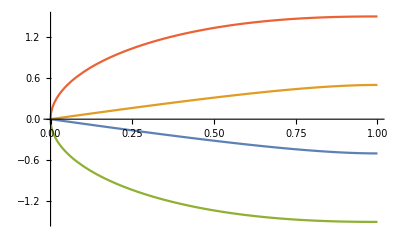

```mathematica
Plot[{-1/2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))),1/2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))),-1/2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))),1/2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2)))},{Γ,0,1}]
```

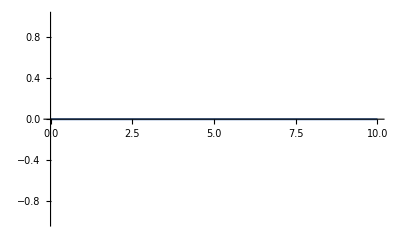

```mathematica
Plot[(-1/2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))^n+(1/2 √(10 Γ-5 Γ^2-2 √(Γ^2 (25-34 Γ+13 Γ^2))))^n+(-1/2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))^n+(1/2 √(10 Γ-5 Γ^2+2 √(Γ^2 (25-34 Γ+13 Γ^2))))^n/.n->7,{Γ,0,1}]
```

```mathematica
Mat1 = {-1*{1,1-Γ,1-Γ},0*{1-Γ,1-Γ,1},1*{1-Γ,1-Γ,1} }
es = Eigensystem[Mat1]
```

{{-1,-1+Γ,-1+Γ},{0,0,0},{1-Γ,1-Γ,1}}

{{0,-√(-(-2+Γ) Γ),√(-(-2+Γ) Γ)},{{1,-(-2+Γ)/(-1+Γ),1},{-(-1-√(-(-2+Γ) Γ))/(-1+Γ),0,1},{-(-1+√(-(-2+Γ) Γ))/(-1+Γ),0,1}}}

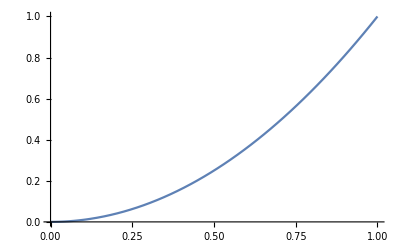

```mathematica
Plot[((-√(-(-2+Γ) Γ))^n+(√(-(-2+Γ) Γ))^n)(1-p)^2 + p^2 /.{n->3, Γ->0.01},{p,0,1}]
```

```mathematica
KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}